```mathematica
求解弹簧摆的运动
```

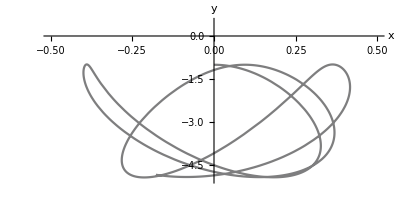

```mathematica
g=9.8;k=0.1;m=0.02;L0=1;tm=10;
xinitial={0,0.5};(*coordinate,velocity*)
yinitial={-L0,0};(*coordinate,velocity*)
equs={m x''[t]==-k x[t] (1-L0/(√(x[t]^2+y[t]^2))),
m y''[t]==k y[t] (-1+L0/(√(x[t]^2+y[t]^2)))-m g,
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,tm},
PlotRange->{{-0.5,0.5},{-5,0.5}},
AxesLabel->{"x","y"},AspectRatio->0.5,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],ColorFunction->Function[{x,y,t},Hue[t]]]
Clear[g,k,m,L0,tm,equs,s,x,y]
```

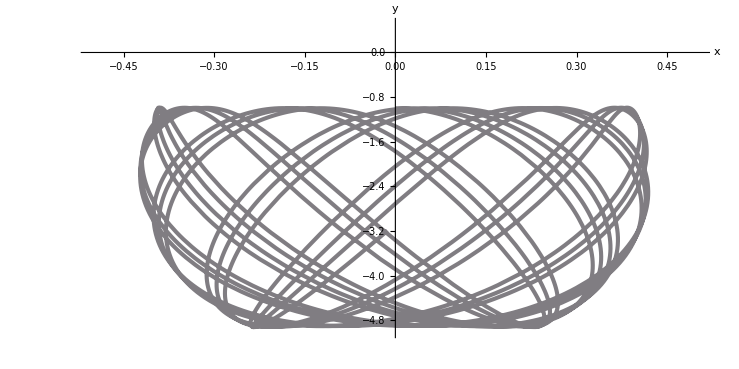

```mathematica
g=9.8;k=0.1;m=0.02;L0=1;tm=50;
xinitial={0,0.5};(*coordinate,velocity*)
yinitial={-L0,0};(*coordinate,velocity*)
equs={m x''[t]==-k x[t] (1-L0/(√(x[t]^2+y[t]^2))),
m y''[t]==k y[t] (-1+L0/(√(x[t]^2+y[t]^2)))-m g,
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,tm},
PlotRange->{{-0.5,0.5},{-5,0.5}},
AxesLabel->{"x","y"},AspectRatio->0.5,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],ColorFunction->Function[{x,y,t},Hue[t]]]
Clear[g,k,m,L0,tm,equs,s,x,y]
```

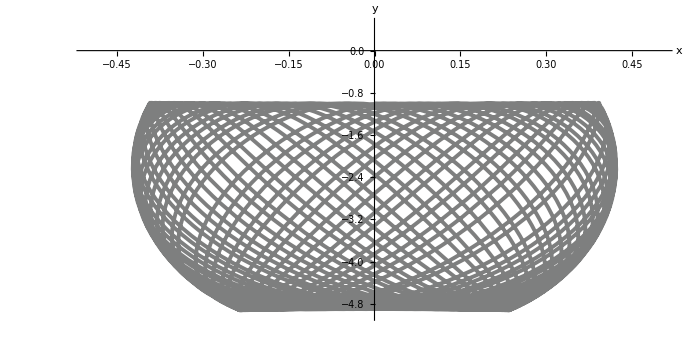

```mathematica
g=9.8;k=0.1;m=0.02;L0=1;tm=100;
xinitial={0,0.5};(*coordinate,velocity*)
yinitial={-L0,0};(*coordinate,velocity*)
equs={m x''[t]==-k x[t] (1-L0/(√(x[t]^2+y[t]^2))),
m y''[t]==k y[t] (-1+L0/(√(x[t]^2+y[t]^2)))-m g,
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,tm},
PlotRange->{{-0.5,0.5},{-5,0.5}},
AxesLabel->{"x","y"},AspectRatio->0.5,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],ColorFunction->Function[{x,y,t},Hue[t]]]
Clear[g,k,m,L0,tm,equs,s,x,y]
```

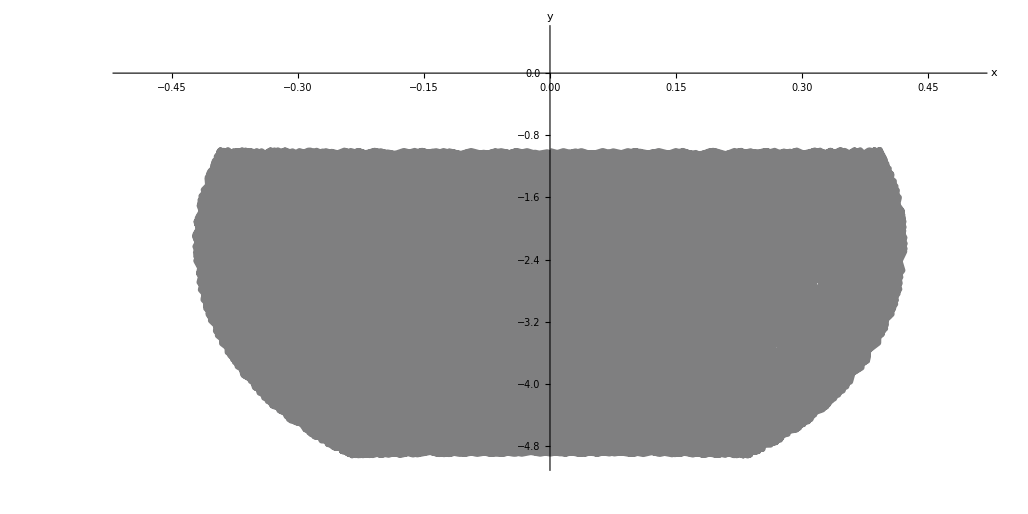

```mathematica
g=9.8;k=0.1;m=0.02;L0=1;tm=1000;
xinitial={0,0.5};(*coordinate,velocity*)
yinitial={-L0,0};(*coordinate,velocity*)
equs={m x''[t]==-k x[t] (1-L0/(√(x[t]^2+y[t]^2))),
m y''[t]==k y[t] (-1+L0/(√(x[t]^2+y[t]^2)))-m g,
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm},MaxSteps->10^6];
{x,y}={x,y}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,tm},
PlotRange->{{-0.5,0.5},{-5,0.5}},
AxesLabel->{"x","y"},AspectRatio->0.5,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],ColorFunction->Function[{x,y,t},Hue[t]]]
Clear[g,k,m,L0,tm,equs,s,x,y]
```